```mathematica
pivot[iStar_, jStar_, tableau_] := (
newTableau = tableau;
numberRows = Dimensions[tableau][[1]];
numberCols = Dimensions[tableau][[2]];
(* switch row tableau variables *)
newTableau[[1,jStar]] = tableau[[iStar, numberCols]];
newTableau[[iStar, numberCols]] = tableau[[1,jStar]];
(* switch column tableau variables *)
newTableau[[numberRows,jStar]] = -tableau[[iStar, 1]];
newTableau[[iStar, 1]] = -tableau[[numberRows,jStar]];
(* adjust loop bounds to skip 1st column and last row *)
For[ii = 2, ii < numberRows, ii++,
For[jj=2,jj<numberCols,jj++,
If[ii == iStar && jj == jStar, 
newTableau[[ii,jj]]=1/tableau[[iStar, jStar]]];
If[ii== iStar && jj ≠ jStar,
newTableau[[ii,jj]]= -tableau[[iStar, jj]]/tableau[[iStar, jStar]]];
If[ii ≠ iStar && jj == jStar,
newTableau[[ii, jj]]= tableau[[ii, jStar]]/tableau[[iStar, jStar]]];
If[ii ≠ iStar && jj ≠ jStar,
newTableau[[ii,jj]] = tableau[[ii,jj]]-tableau[[iStar,jj]]*tableau[[ii, jStar]]/tableau[[iStar,jStar]]];
]
];
Return[newTableau];
)
```

```mathematica
(* The given LP:

*)
```

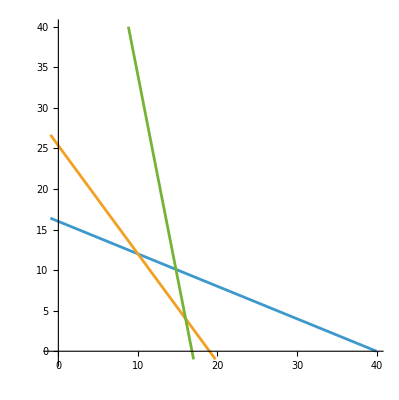

```mathematica
(* Part 1 graph feasible region. Shading is optional. *)
Clear[x1,x2]
z[x1_,x2_]:=16x1+19x2-10
g1[x1_,x2_]:=2x1+5x2
g2[x1_,x2_]:=4x1+3x2
g3[x1_,x2_]:=5x1+1x2
delz={16,19}; (* gradient of z *)
delg1={2,5};(* gradient of g1 *)
delg2={4,3};(* gradient of g2 *)
delg3={5,1}; (* gradient of g3 *)
b1=80;
b2=76;
b3=84;
db1=0;
db2=0;
db3=0;
g1[x1_]:=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]]
g2[x1_]:=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]]
g3[x1_]:=x2/.Solve[g3[x1,x2]==b3,{x2}][[1,1]]

Plot[{g1[x],g2[x],g3[x]},{x,-1,40},AspectRatio->Automatic,PlotRange->{-1,40},PlotHighlighting->None ]
```

```mathematica
(* Part 2 *)
(* solve baseline tableau *)
db1=0;
db2=0;
db3=0;
m0={" ","y1","y2","y3",1," "};
m1={"x1",2,4,5,-16,"v1"};
m2={"x2",5,3,1,-19,"v2"}; 
mobj={-1,b1+db1,b2+db2,b3+db3,-10,"w→min"};
mLast={"",-"s1",-"s2",-"s3","-z→min" ,""};
a={m0,m1,m2,mobj,mLast};
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[a]];
b=pivot[2,2,a]; 
MatrixForm[b];
c=pivot[2,3,b];
MatrixForm[c];
d=pivot[3,3,c];
Print["db = ( ",db1," ",db2," ",db3," ) optimal = ",MatrixForm[d] ]
```

db = ( 0 0 0 ) initial = (  | y1 | y2 | y3 | 1 |  
x1 | 2 | 4 | 5 | -16 | v1
x2 | 5 | 3 | 1 | -19 | v2
-1 | 80 | 76 | 84 | -10 | w→min
 | -s1 | -s2 | -s3 | -z→min | )

db = ( 0 0 0 ) optimal = (  | v1 | v2 | y3 | 1 |  
s2 | 5/14 | -1/7 | -23/14 | 3 | y2
s1 | -3/14 | 2/7 | 11/14 | 2 | y1
-1 | 10 | 12 | 22 | 378 | w→min
 | -x1 | -x2 | -s3 | -z→min | )

```mathematica
(* primal solution FOR THE BASELINE CASE before the Part 5 variations *)
zStarBase=378;
x1StarBase=10;x2StarBase=12;
xStarBase={x1StarBase,x2StarBase};
(* dual solution *)
wStar=378;
y1Star=2;y2Star=3;y3Star=0;
yStar={y1Star,y2Star,y3Star};
(* for convenience define shorter variable names for yStar *)
y1=y1Star; y2=y2Star; y3=y3Star; 
y={y1,y2,y3};
```

```mathematica
(* Part 3 *)
```

```mathematica
Solve[g1[u,v] == b1 && g3[u,v] == b3]
```

{{u→340/23,v→232/23}}

```mathematica
b2Max = g2[340/23, 232/23]
```

2056/23

```mathematica
db2Max = 2056/23
```

2056/23

```mathematica
(* Part 4 *)
```

```mathematica
(* db = db1 db2 db3 

*)
```

```mathematica
(* 4.a *)
db1=0;
db2=2;
db3=0;
(* resCost=p1 (b1+db1)+p2 (b2+db2)+p3 (b3+db3) *)
m0={" ","y1","y2","y3",1," "};
m1={"x1",2,4,5,-16,"v1"};
m2={"x2",5,3,1,-19,"v2"}; 
mobj={-1,b1+db1,b2+db2,b3+db3,-10,"w→min"};
mLast={"",-"s1",-"s2",-"s3","-z→min" ,""};
a={m0,m1,m2,mobj,mLast};
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[a]];
b=pivot[2,2,a]; 
MatrixForm[b];(* supress output except for optimal tableau *)
c=pivot[2,3,b];
MatrixForm[c];
d=pivot[3,3,c];
MatrixForm[d];
Print["db = ( ",db1," ",db2," ",db3," ) optimal = ",MatrixForm[d] ]
```

db = ( 0 2 0 ) initial = (  | y1 | y2 | y3 | 1 |  
x1 | 2 | 4 | 5 | -16 | v1
x2 | 5 | 3 | 1 | -19 | v2
-1 | 80 | 78 | 84 | -10 | w→min
 | -s1 | -s2 | -s3 | -z→min | )

db = ( 0 2 0 ) optimal = (  | v1 | v2 | y3 | 1 |  
s2 | 5/14 | -1/7 | -23/14 | 3 | y2
s1 | -3/14 | 2/7 | 11/14 | 2 | y1
-1 | 75/7 | 82/7 | 131/7 | 384 | w→min
 | -x1 | -x2 | -s3 | -z→min | )

```mathematica
(* read new x & z from each new optimal tableau and verify relations *) 
Print["xStarNew = ",xStarNew ={75/7,82/7}]
Print["zStarNew = ",zStarNew=384]
Print["dxStar = ",dxStar=xStarNew-xStarBase]
Print["dzStar = ",dzStar = zStarNew-zStarBase]
dzStar==delz.dxStar==(y1Star delg1+y2Star delg2+y3Star delg3).dxStar==y1Star(delg1.dxStar)+y2Star(delg2.dxStar)+y3Star(delg3.dxStar)==y1Star db1+y2Star db2+y3Star db3
```

xStarNew = {75/7,82/7}

zStarNew = 384

dxStar = {5/7,-2/7}

dzStar = 6

True

```mathematica
(* 4.b *)
db1=3;
db2=0;
db3=0;
m0={" ","y1","y2","y3",1," "};
m1={"x1",2,4,5,-16,"v1"};
m2={"x2",5,3,1,-19,"v2"}; 
mobj={-1,b1+db1,b2+db2,b3+db3,-10,"w→min"};
mLast={"",-"s1",-"s2",-"s3","-z→min" ,""};
a={m0,m1,m2,mobj,mLast};
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[a]];
(* 1st pivot *)
b=pivot[2,2,a]; 
MatrixForm[b];(* supress output except for optimal tableau *)
c=pivot[2,3,b];
MatrixForm[c];
d=pivot[3,3,c];
MatrixForm[d];
Print["db = ( ",db1," ",db2," ",db3," ) optimal = ",MatrixForm[d] ]
```

db = ( 3 0 0 ) initial = (  | y1 | y2 | y3 | 1 |  
x1 | 2 | 4 | 5 | -16 | v1
x2 | 5 | 3 | 1 | -19 | v2
-1 | 83 | 76 | 84 | -10 | w→min
 | -s1 | -s2 | -s3 | -z→min | )

db = ( 3 0 0 ) optimal = (  | v1 | v2 | y3 | 1 |  
s2 | 5/14 | -1/7 | -23/14 | 3 | y2
s1 | -3/14 | 2/7 | 11/14 | 2 | y1
-1 | 131/14 | 90/7 | 341/14 | 384 | w→min
 | -x1 | -x2 | -s3 | -z→min | )

```mathematica
(* read new x & z from each new optimal tableau and verify relations *) 
Print["xStarNew = ",xStarNew ={131/14,90/7}]
Print["zStarNew = ",zStarNew=384]
Print["dxStar = ",dxStar=xStarNew-xStarBase]
Print["dzStar = ",dzStar = zStarNew-zStarBase]
dzStar==delz.dxStar==(y1Star delg1+y2Star delg2+y3Star delg3).dxStar==y1Star(delg1.dxStar)+y2Star(delg2.dxStar)+y3Star(delg3.dxStar)==y1Star db1+y2Star db2+y3Star db3
```

xStarNew = {131/14,90/7}

zStarNew = 384

dxStar = {-9/14,6/7}

dzStar = 6

True

```mathematica
(* 4.c *)
db1=3;
db2=2;
db3=0;
m0={" ","y1","y2","y3",1," "};
m1={"x1",2,4,5,-16,"v1"};
m2={"x2",5,3,1,-19,"v2"}; 
mobj={-1,b1+db1,b2+db2,b3+db3,-10,"w→min"};
mLast={"",-"s1",-"s2",-"s3","-z→min" ,""};
a={m0,m1,m2,mobj,mLast};
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[a]];
b=pivot[2,2,a]; 
MatrixForm[b];(* supress output except for optimal tableau *)
c=pivot[2,3,b];
MatrixForm[c];
d=pivot[3,3,c];
MatrixForm[d];
Print["db = ( ",db1," ",db2," ",db3," ) optimal = ",MatrixForm[d] ]
```

db = ( 3 2 0 ) initial = (  | y1 | y2 | y3 | 1 |  
x1 | 2 | 4 | 5 | -16 | v1
x2 | 5 | 3 | 1 | -19 | v2
-1 | 83 | 78 | 84 | -10 | w→min
 | -s1 | -s2 | -s3 | -z→min | )

db = ( 3 2 0 ) optimal = (  | v1 | v2 | y3 | 1 |  
s2 | 5/14 | -1/7 | -23/14 | 3 | y2
s1 | -3/14 | 2/7 | 11/14 | 2 | y1
-1 | 141/14 | 88/7 | 295/14 | 390 | w→min
 | -x1 | -x2 | -s3 | -z→min | )

```mathematica
(* read new x & z from each new optimal tableau and verify relations *) 
Print["xStarNew = ",xStarNew ={141/14,88/7}]
Print["zStarNew = ",zStarNew=390]
Print["dxStar = ",dxStar=xStarNew-xStarBase]
Print["dzStar = ",dzStar = zStarNew-zStarBase]
dzStar==delz.dxStar==(y1Star delg1+y2Star delg2+y3Star delg3).dxStar==y1Star(delg1.dxStar)+y2Star(delg2.dxStar)+y3Star(delg3.dxStar)==y1Star db1+y2Star db2+y3Star db3
```

xStarNew = {141/14,88/7}

zStarNew = 390

dxStar = {1/14,4/7}

dzStar = 12

True

```mathematica
(* 4.d *)
db1=15;
db2=-4;
db3=0;
m0={" ","y1","y2","y3",1," "};
m1={"x1",2,4,5,-16,"v1"};
m2={"x2",5,3,1,-19,"v2"}; 
mobj={-1,b1+db1,b2+db2,b3+db3,-10,"w→min"};
mLast={"",-"s1",-"s2",-"s3","-z→min" ,""};
a={m0,m1,m2,mobj,mLast};
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[a]];
b=pivot[2,2,a]; 
MatrixForm[b];(* supress output except for optimal tableau *)
c=pivot[2,3,b];
MatrixForm[c];
d=pivot[3,3,c];
MatrixForm[d];
Print["db = ( ",db1," ",db2," ",db3," ) optimal = ",MatrixForm[d] ]
```

db = ( 5 -4 0 ) initial = (  | y1 | y2 | y3 | 1 |  
x1 | 2 | 4 | 5 | -16 | v1
x2 | 5 | 3 | 1 | -19 | v2
-1 | 85 | 72 | 84 | -10 | w→min
 | -s1 | -s2 | -s3 | -z→min | )

db = ( 5 -4 0 ) optimal = (  | v1 | v2 | y3 | 1 |  
s2 | 5/14 | -1/7 | -23/14 | 3 | y2
s1 | -3/14 | 2/7 | 11/14 | 2 | y1
-1 | 15/2 | 14 | 65/2 | 376 | w→min
 | -x1 | -x2 | -s3 | -z→min | )

```mathematica
(* read new x & z from each new optimal tableau and verify relations *) 
Print["xStarNew = ",xStarNew ={15/2,14}]
Print["zStarNew = ",zStarNew=376]
Print["dxStar = ",dxStar=xStarNew-xStarBase]
Print["dzStar = ",dzStar = zStarNew-zStarBase]
dzStar==delz.dxStar==(y1Star delg1+y2Star delg2+y3Star delg3).dxStar==y1Star(delg1.dxStar)+y2Star(delg2.dxStar)+y3Star(delg3.dxStar)==y1Star db1+y2Star db2+y3Star db3
```

xStarNew = {15/2,14}

zStarNew = 376

dxStar = {-5/2,2}

dzStar = -2

True

```mathematica
db1=0;
db2=308/23; (*actual db2Max, mine is wrong some reason*)
db3=0;
m0={" ","y1","y2","y3",1," "};
m1={"x1",2,4,5,-16,"v1"};
m2={"x2",5,3,1,-19,"v2"}; 
mobj={-1,b1+db1,b2+db2,b3+db3,-10,"w→min"};
mLast={"",-"s1",-"s2",-"s3","-z→min" ,""};
a={m0,m1,m2,mobj,mLast};
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[a]];
b=pivot[2,2,a]; 
MatrixForm[b];(* supress output except for optimal tableau *)
c=pivot[2,3,b];
MatrixForm[c];
d=pivot[3,3,c];
MatrixForm[d];
Print["db = ( ",db1," ",db2," ",db3," ) optimal = ",MatrixForm[d] ]
```

db = ( 0 308/23 0 ) initial = (  | y1 | y2 | y3 | 1 |  
x1 | 2 | 4 | 5 | -16 | v1
x2 | 5 | 3 | 1 | -19 | v2
-1 | 80 | 2056/23 | 84 | -10 | w→min
 | -s1 | -s2 | -s3 | -z→min | )

db = ( 0 308/23 0 ) optimal = (  | v1 | v2 | y3 | 1 |  
s2 | 5/14 | -1/7 | -23/14 | 3 | y2
s1 | -3/14 | 2/7 | 11/14 | 2 | y1
-1 | 340/23 | 232/23 | 0 | 9618/23 | w→min
 | -x1 | -x2 | -s3 | -z→min | )

```mathematica
(*level set example, pivot on y3, y2*)
e =pivot[3,4, d]
Print["db = ( ",db1," ",db2," ",db3," ) optimal = ",MatrixForm[e] ]
```

{{ ,v1,v2,y1,1, },{s2,-1/11,5/11,-23/11,79/11,y2},{s3,3/11,-4/11,14/11,-28/11,y3},{-1,340/23,232/23,0,9618/23,w→min},{,-x1,-x2,-s1,-z→min,}}

db = ( 0 308/23 0 ) optimal = (  | v1 | v2 | y1 | 1 |  
s2 | -1/11 | 5/11 | -23/11 | 79/11 | y2
s3 | 3/11 | -4/11 | 14/11 | -28/11 | y3
-1 | 340/23 | 232/23 | 0 | 9618/23 | w→min
 | -x1 | -x2 | -s1 | -z→min | )